## 2 eint matrix

```mathematica
getColour[sym_]:=Module[{r,g,b},
r=0;
g=0;
b=0;
Which[
(sym==1), r=1,
(sym==2),g=1,
(sym==3),b=1,
(1==1),r=1;g=1;b=1
];
{r,g,b}
]
boxColour[l_,m_]:=Which[((l==1) &&(m==1)),Red, ((l==2) &&(m==1)), Green,((l==2) &&(m==2)), Blue,(1==1),White]
```

```mathematica
basebox[L_,M_,P_,Q_,R_,S_,I_,x_,y_]:={EdgeForm[Thin],RGBColor[getColour[L] + getColour[M]],Rectangle[{x,y}],
Black,
Text[L,{.25+x,(3/4+1/8)+y}],Text[M,{.75+x,(3/4+1/8)+y}],
Text[P,{.25+x,(2/4+1/8)+y}],Text[Q,{.75+x,(2/4+1/8)+y}],
Text[R,{.25+x,(1/4+1/8)+y}],Text[S,{.75+x,(1/4+1/8)+y}],
Text[I,{.50+x,(0/4+1/8)+y}]}
```

```mathematica
Export["/Users/dylan/thesis/pres_figs/2_eint_mat.pdf",Graphics[{basebox[1,1,1,1,1,1,1,0,0],basebox[1,1,2,1,1,1,2,1,0],basebox[1,1,2,2,1,1,4,2,0],basebox[1,1,3,1,1,1,7,3,0],basebox[1,1,3,2,1,1,11,4,0],basebox[1,1,3,3,1,1,16,5,0],
basebox[2,1,1,1,1,1,22,6,0],basebox[2,1,2,1,1,1,29,7,0],basebox[2,1,2,2,1,1,37,8,0],
basebox[1,1,2,1,2,1,3,1,-1],basebox[1,1,2,2,2,1,5,2,-1],basebox[1,1,3,1,2,1,8,3,-1],basebox[1,1,3,2,2,1,12,4,-1],basebox[1,1,3,3,2,1,17,5,-1],basebox[2,1,1,1,2,1,23,6,-1],basebox[2,1,2,1,2,1,30,7,-1],basebox[2,1,2,2,2,1,38,8,-1],
basebox[1,1,2,2,2,2,6,2,-2],basebox[1,1,3,1,2,2,9,3,-2],basebox[1,1,3,2,2,2,13,4,-2],basebox[1,1,3,3,2,2,18,5,-2],basebox[2,1,1,1,2,2,24,6,-2],basebox[2,1,2,1,2,2,31,7,-2],basebox[2,1,2,2,2,2,39,8,-2],
basebox[1,1,3,1,3,1,10,3,-3],basebox[1,1,3,2,3,1,14,4,-3],basebox[1,1,3,3,3,1,19,5,-3],basebox[2,1,1,1,3,1,25,6,-3],basebox[2,1,2,1,3,1,32,7,-3],basebox[2,1,2,2,3,1,40,8,-3],
basebox[1,1,3,2,3,2,15,4,-4],basebox[1,1,3,3,3,2,20,5,-4],basebox[2,1,1,1,3,2,26,6,-4],basebox[2,1,2,1,3,2,33,7,-4],basebox[2,1,2,2,3,2,41,8,-4],
basebox[1,1,3,3,3,3,21,5,-5],basebox[2,1,1,1,3,3,27,6,-5],basebox[2,1,2,1,3,3,34,7,-5],basebox[2,1,2,2,3,3,42,8,-5],
basebox[2,2,1,1,1,1,28,6,-6],basebox[2,2,2,1,1,1,35,7,-6],basebox[2,2,2,2,1,1,43,8,-6],
basebox[2,2,2,1,2,1,36,7,-7],basebox[2,2,2,2,2,1,44,8,-7],
basebox[2,2,2,2,2,2,45,8,-8], basebox["λ","μ","p","q","r","s","i",0,-8]}, BaseStyle->{FontSize->50,FontFamily->"Times"},ImageSize->2000]
]
```

/Users/dylan/thesis/pres_figs/2_eint_mat.pdf

```mathematica
Graphics[{basebox[1,1,1,1,1,1,1,0,0],basebox[1,1,2,1,1,1,2,1,0],basebox[1,1,2,2,1,1,4,2,0],basebox[1,1,3,1,1,1,7,3,0],basebox[1,1,3,2,1,1,11,4,0],basebox[1,1,3,3,1,1,16,5,0],
basebox[2,1,1,1,1,1,22,6,0],basebox[2,1,2,1,1,1,29,7,0],basebox[2,1,2,2,1,1,37,8,0],
basebox[1,1,2,1,2,1,3,1,-1],basebox[1,1,2,2,2,1,5,2,-1],basebox[1,1,3,1,2,1,8,3,-1],basebox[1,1,3,2,2,1,12,4,-1],basebox[1,1,3,3,2,1,17,5,-1],basebox[2,1,1,1,2,1,23,6,-1],basebox[2,1,2,1,2,1,30,7,-1],basebox[2,1,2,2,2,1,38,8,-1],
basebox[1,1,2,2,2,2,6,2,-2],basebox[1,1,3,1,2,2,9,3,-2],basebox[1,1,3,2,2,2,13,4,-2],basebox[1,1,3,3,2,2,18,5,-2],basebox[2,1,1,1,2,2,24,6,-2],basebox[2,1,2,1,2,2,31,7,-2],basebox[2,1,2,2,2,2,39,8,-2],
basebox[1,1,3,1,3,1,10,3,-3],basebox[1,1,3,2,3,1,14,4,-3],basebox[1,1,3,3,3,1,19,5,-3],basebox[2,1,1,1,3,1,25,6,-3],basebox[2,1,2,1,3,1,32,7,-3],basebox[2,1,2,2,3,1,40,8,-3],
basebox[1,1,3,2,3,2,15,4,-4],basebox[1,1,3,3,3,2,20,5,-4],basebox[2,1,1,1,3,2,26,6,-4],basebox[2,1,2,1,3,2,33,7,-4],basebox[2,1,2,2,3,2,41,8,-4],
basebox[1,1,3,3,3,3,21,5,-5],basebox[2,1,1,1,3,3,27,6,-5],basebox[2,1,2,1,3,3,34,7,-5],basebox[2,1,2,2,3,3,42,8,-5],
basebox[2,2,1,1,1,1,28,6,-6],basebox[2,2,2,1,1,1,35,7,-6],basebox[2,2,2,2,1,1,43,8,-6],
basebox[2,2,2,1,2,1,36,7,-7],basebox[2,2,2,2,2,1,44,8,-7],
basebox[2,2,2,2,2,2,45,8,-8], basebox["L","M","P","Q","R","S","I",0,-8]}, BaseStyle->{FontSize->20,FontFamily->"Times"}]
```

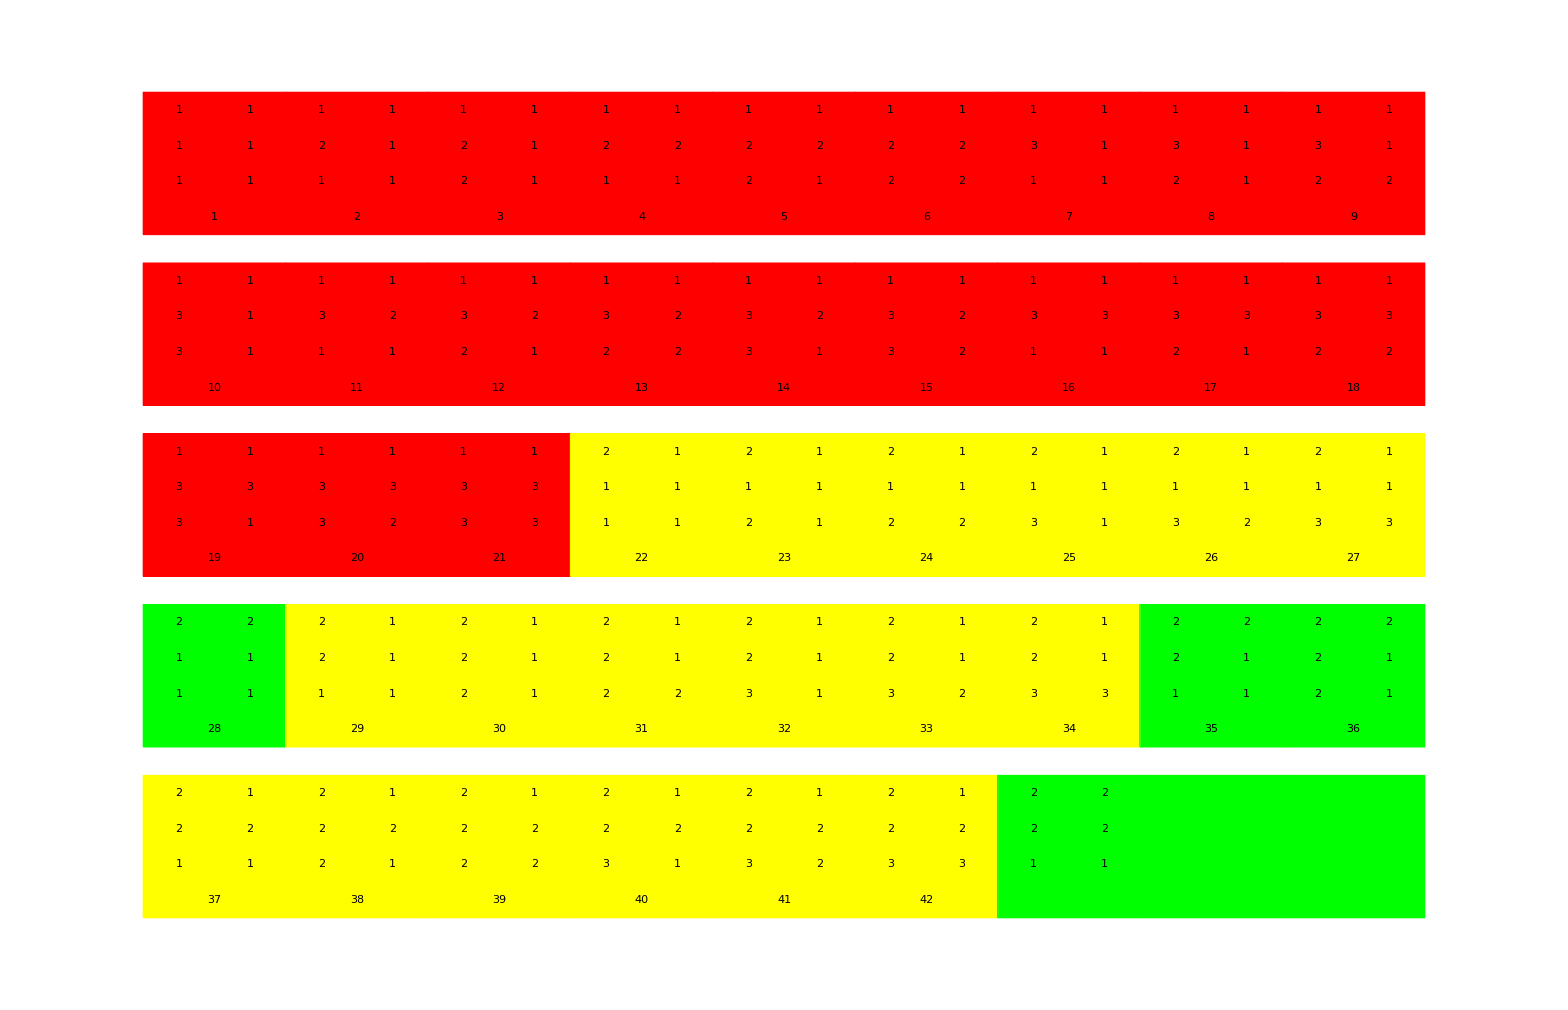

/Users/dylan/thesis/pres_figs/2eint_vec.pdf

```mathematica
nbs={3,2};
i=0;
x=0;
y=0;
all={};
For[l=1,l≤2,l++,
For[p=1,p≤nbs[[l]],p++,
For[q=1,q≤p,q++,
For[m=1,m≤l,m++,
If[l==m,maxr=p,maxr=nbs[[m]]];
For[r=1,r≤maxr,r++,
If[(l==m) &&(p==r),maxs=q,maxs=r];
For[s=1,s≤maxs,s++,
i++;
If[Mod[x,9]==0,{x=0;y--}];
x++;
all=Append[all,basebox[l,m,p,q,r,s,i,x,y + (0.2 * y)]];
]
]
]
]
]
]
y--;
Graphics[all,BaseStyle->{FontSize->50,FontFamily->"Times"},ImageSize->2000]
Export["/Users/dylan/thesis/pres_figs/2eint_vec.pdf",Graphics[all,BaseStyle->{FontSize->50,FontFamily->"Times"},ImageSize->2000]]
```

## Density matrix

```mathematica
boxColourD[sx_,sy_,text_]:=Which[text,White,(sx && sy),Green, (sx||sy), Yellow,(!sx&&!sy), Cyan]
baseboxD[R_,S_,I_,x_,y_,sx_,sy_,nbs_,text_]:={EdgeForm[Thin],boxColourD[sx,sy,text],Rectangle[{x,y}],
Black,
Text[Which[text, Superscript[R,"x"],sx,Superscript[R-nbs,"S"],!sx,Superscript[R,"L"]],{.25+x,(2/3)+y}],Text[Which[text, Superscript[S,"x"],sy,Superscript[S-nbs,"S"],!sy,Superscript[S,"L"]],{.75+x,(2/3)+y}],
Text[I,{.50+x,(1/3)+y}]}
Graphics[baseboxD[1,1,1,1,1,True, False,nbs,True],BaseStyle->{FontSize->20,FontFamily->"Times"}]
```

-Graphics-

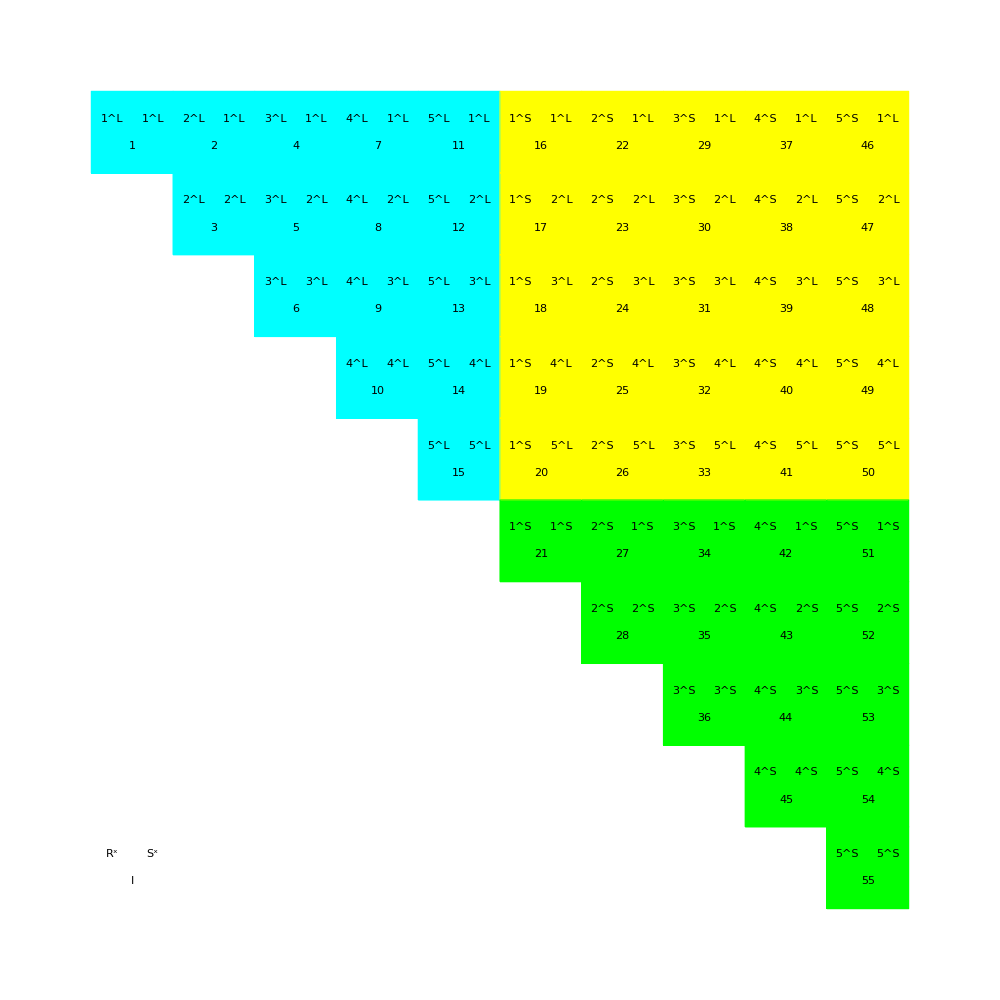

```mathematica
nbs=5;
i=0;
x=0;
y=0;
sx=False;
sy=False;
ymax=-1;
all={};
For[r=1,r≤nbs*2,r++,
For[s=1,s≤r,s++,
i++;
If[y==ymax,y=0;x++;ymax--;];
If[r>nbs, sx=True,sx=False];
If[s>nbs, sy=True,sy=False];
all=Append[all,baseboxD[r,s,i,x,y ,sx,sy,nbs,False]];
y--;
]
]
y++;
all=Append[all,baseboxD["R","S","I",0,y ,False,False,nbs,True]];
Graphics[all,BaseStyle->{FontSize->20,FontFamily->"Times"},ImageSize->1000]
```

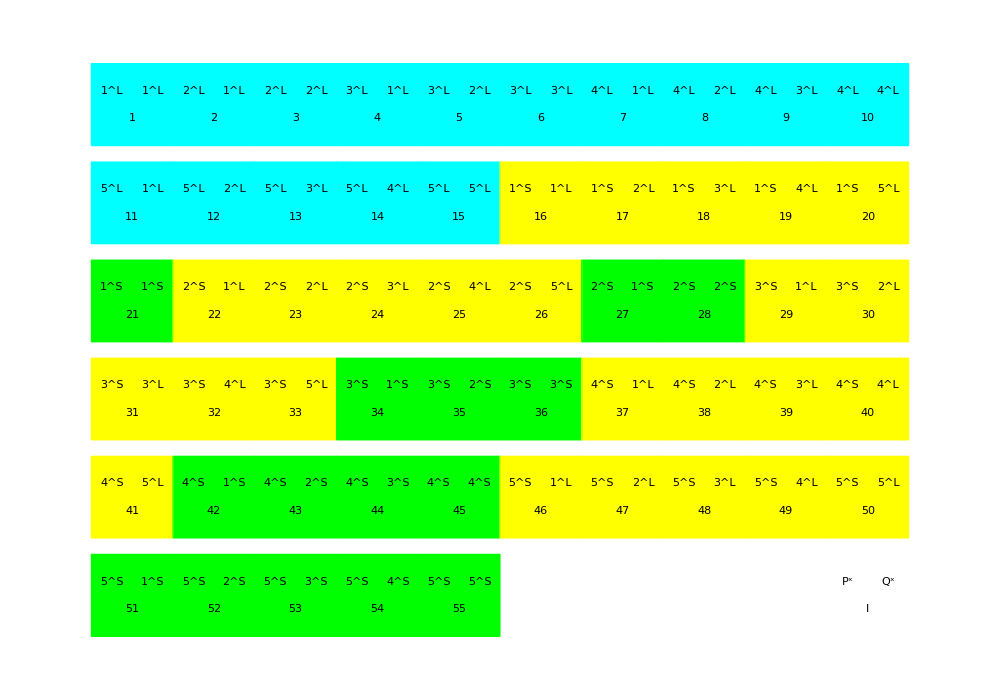

```mathematica
nbs=5;
i=0;
x=0;
y=0;
sx=False;
sy=False;
xmax=9;
all={};
For[r=1,r≤nbs*2,r++,
For[s=1,s≤r,s++,
i++;
If[r>nbs, sx=True,sx=False];
If[s>nbs, sy=True,sy=False];
all=Append[all,baseboxD[r,s,i,x,y +(y*0.2),sx,sy,nbs,False]];
If[x==xmax,x=0;y--;,x++];
]
]
all=Append[all,baseboxD["P","Q","I",9,y +(y*0.2),False,False,nbs,True]];
Graphics[all,BaseStyle->{FontSize->20,FontFamily->"Times"},ImageSize->1000]
```

## Lots of BFs

```mathematica
boxColourDLots[sx_,sy_,text_]:=Which[text,White,(sx && sy),Green, (sx||sy), Yellow,(!sx&&!sy), Cyan]
baseboxDLots[R_,S_,I_,x_,y_,sx_,sy_,nbs_,text_]:={EdgeForm[Thin],boxColourDLots[sx,sy,text],Rectangle[{x,y}],
Black}
getColour[sym_]:=Module[{r,g,b},
r=0;
g=0;
b=0;
Which[
(sym==1), r=1,
(sym==2),g=1,
(sym==3),b=1
];
{r,g,b}
]
baseboxLots[L_,M_,x_,y_]:={EdgeForm[Thin],RGBColor[getColour[L] + getColour[M]],Rectangle[{x,y}],
Black}
```

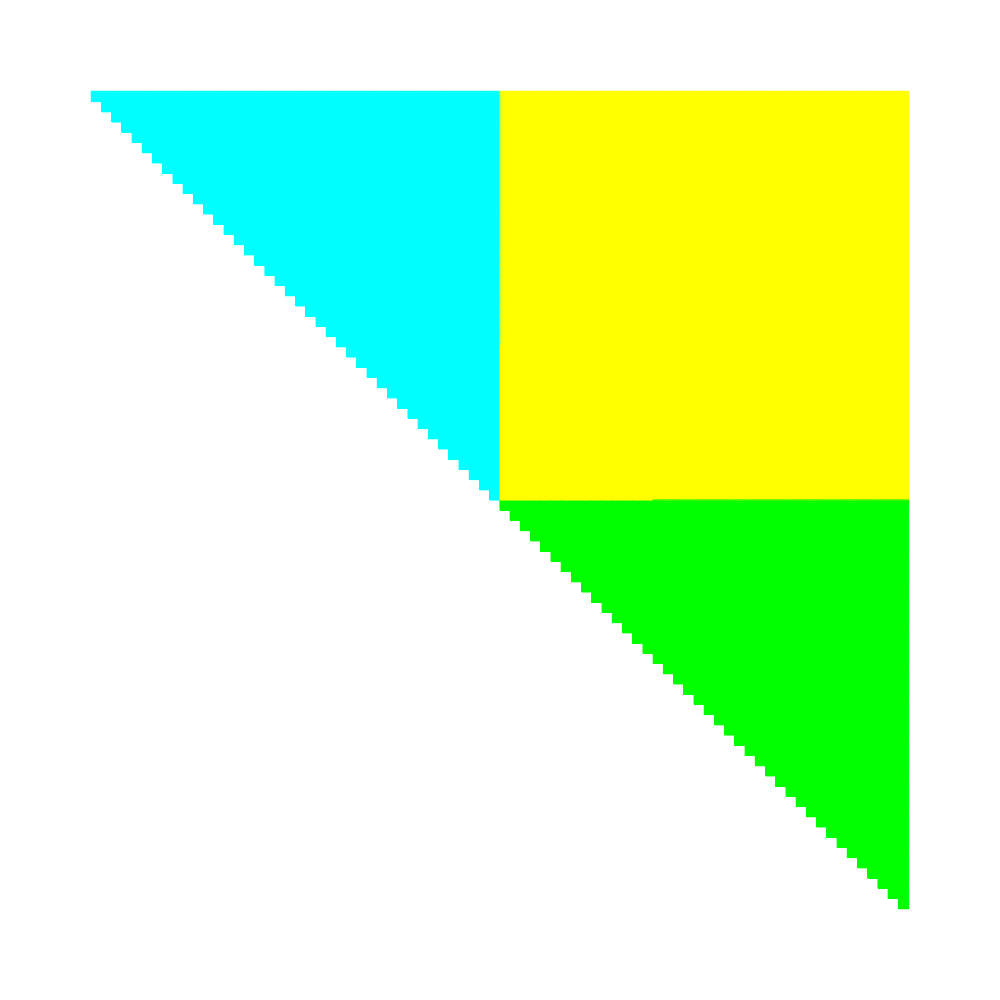

```mathematica
nbs=40;
i=0;
x=0;
y=0;
sx=False;
sy=False;
ymax=-1;
all={};
For[r=1,r≤nbs*2,r++,
For[s=1,s≤r,s++,
i++;
If[y==ymax,y=0;x++;ymax--;];
If[r>nbs, sx=True,sx=False];
If[s>nbs, sy=True,sy=False];
all=Append[all,baseboxDLots[r,s,i,x,y ,sx,sy,nbs,False]];
y--;
]
]
Graphics[all,ImageSize->1000]
```

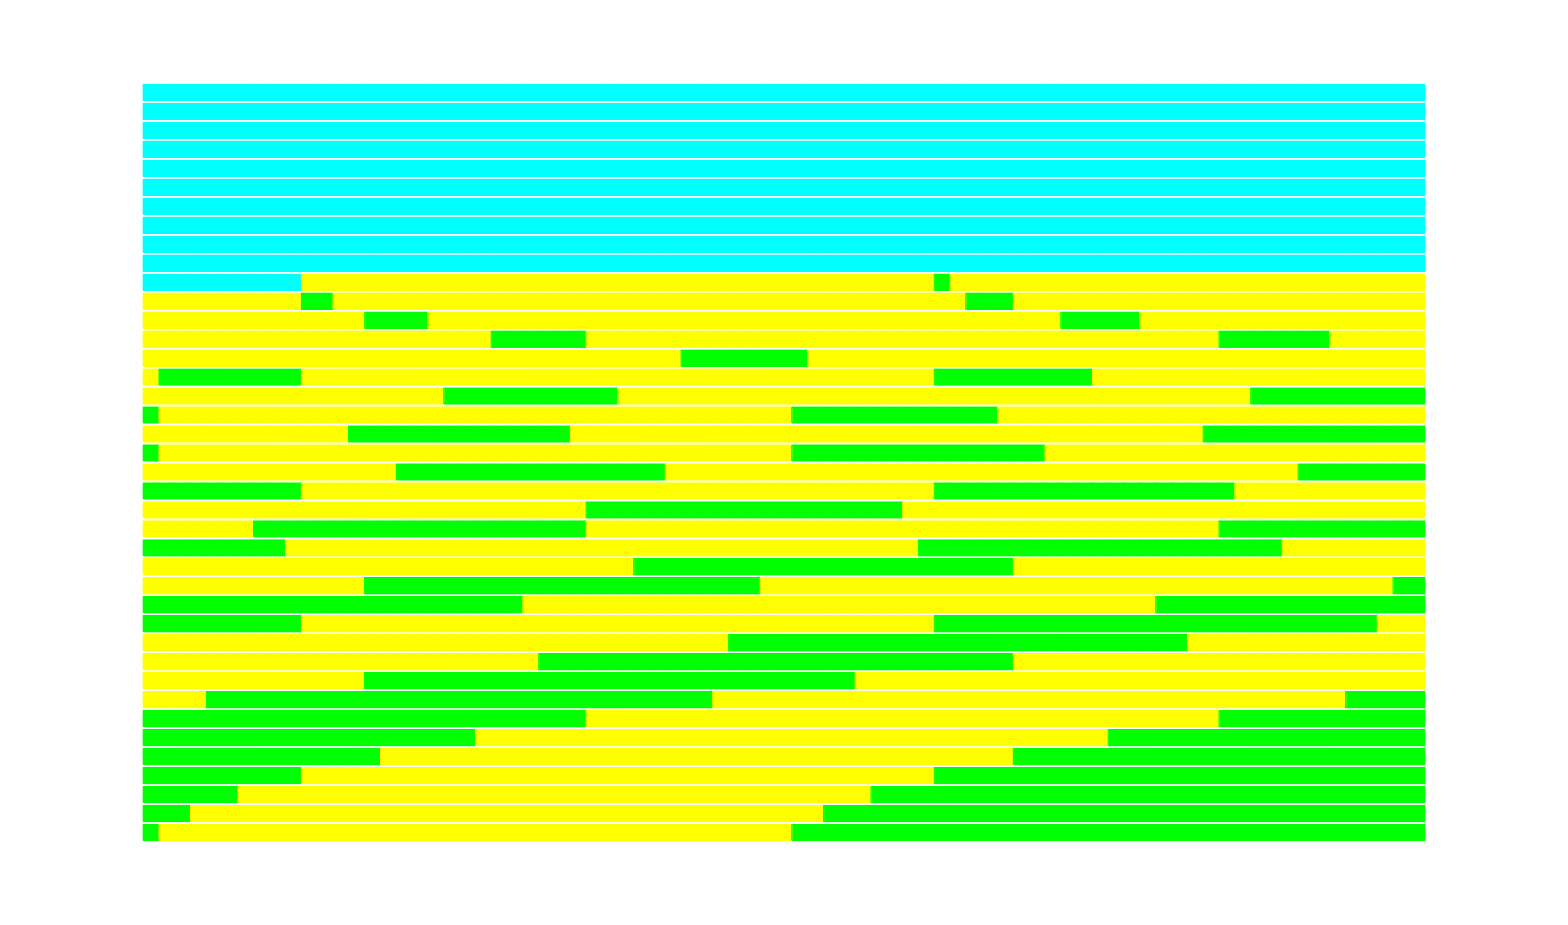

```mathematica
nbs=40;
i=0;
x=0;
y=0;
sx=False;
sy=False;
xmax=80;
all={};
For[r=1,r≤nbs*2,r++,
For[s=1,s≤r,s++,
i++;
If[r>nbs, sx=True,sx=False];
If[s>nbs, sy=True,sy=False];
all=Append[all,baseboxDLots[r,s,i,x,y +(y*0.2),sx,sy,nbs,False]];
If[x==xmax,x=0;y--;,x++];
]
]
Graphics[all,ImageSize->2000]
```

```mathematica
nbs={10,10,10};
i=0;
x=0;
y=0;
ymax=-1;
all={};
For[l=1,l≤3,l++,
For[p=1,p≤nbs[[l]],p++,
For[q=1,q≤p,q++,
For[m=1,m≤l,m++,
If[l==m,maxr=p,maxr=nbs[[m]]];
For[r=1,r≤maxr,r++,
If[(l==m) &&(p==r),maxs=q,maxs=r];
For[s=1,s≤maxs,s++,
i++;
If[y==ymax,y=0;x++;ymax--;];
If[r>nbs, sx=True,sx=False];
If[s>nbs, sy=True,sy=False];
all=Append[all,baseboxLots[l,m,x,y ]];
y--;
]
]
]
]
]
]
```

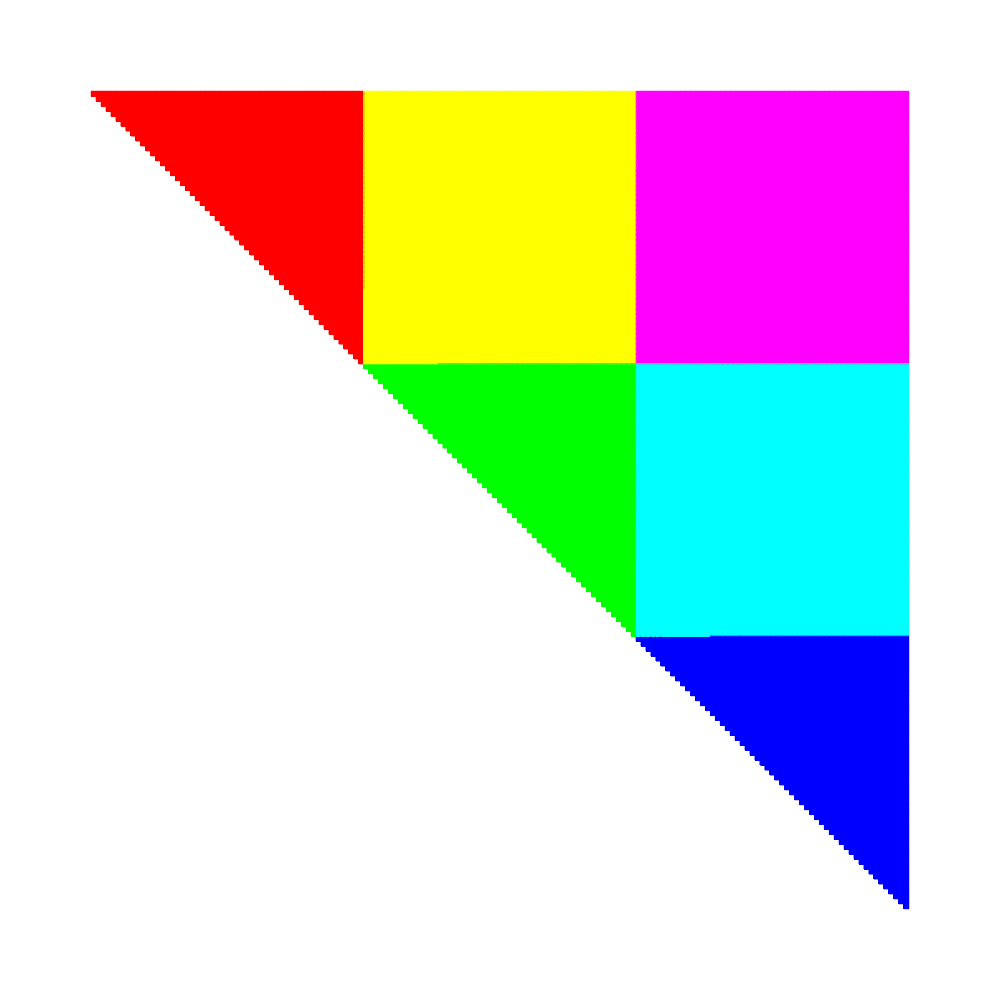

```mathematica
Graphics[{all,{EdgeForm[{Thick,Green}],Transparent,Rectangle[{0,1},{165,0}]}},ImageSize->1000]
```

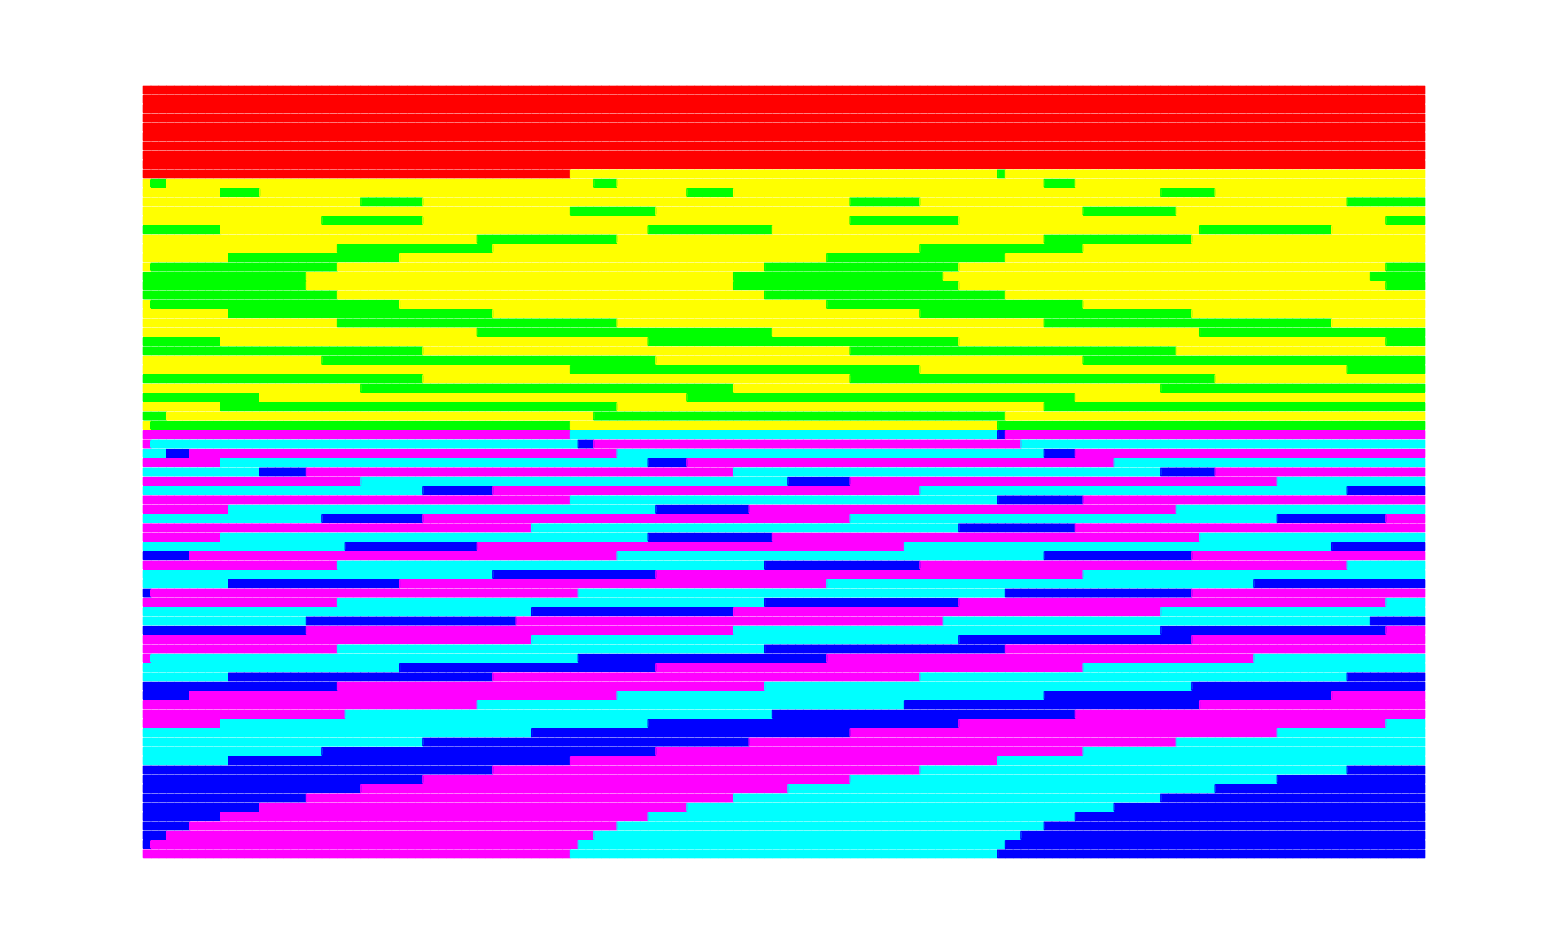

13695

-83

```mathematica
nbs={10,10,10};
i=0;
x=0;
y=0;
xmax=164;
all={};
For[l=1,l≤3,l++,
For[p=1,p≤nbs[[l]],p++,
For[q=1,q≤p,q++,
For[m=1,m≤l,m++,
If[l==m,maxr=p,maxr=nbs[[m]]];
For[r=1,r≤maxr,r++,
If[(l==m) &&(p==r),maxs=q,maxs=r];
For[s=1,s≤maxs,s++,
i++;
all=Append[all,baseboxLots[l,m,x,y +(y*0.2)]];
If[(m==1)&&(r==1)&&(r==s),all=Append[all,{EdgeForm[{Thick,Green}],Transparent,Rectangle[{x,y +(y*0.2)}]}]];
If[x==xmax,x=0;y--;,x++];
]
]
]
]
]
]
Graphics[all,ImageSize->2000]
i
y
```

## Profiling info

```mathematica
(*all times are in ms unless otherwise noted*)
n2eints={
74305,
353220,
1081185,
2588950,
5299140,
9726255,
16476670,
26248635
};
eint2gpuT={
4.6821,
18.056,
52.512,
118.2,
237.96,
437.88,
730.24,
1159.98
}; (*millisecs*)
lmpqrsArrayT={
0.18406,
0.71441,
2.2137,
5.3615,
11.076,
20.818,
35.962,
57.998
};
eint2cpuT={
59.9956,
320.001,
980,
2360,
4910,
8880,
15140,
24180
};(*millisecs*)
formpqCpuIter={
21,
19,
19,
19,
19,
24,
26,
24
};
formpqCpuT={
39.997,
110,
350,
750,
1540,
3660,
6930,
10230
};(*total time per run*)
cpuTotalT={
0.124,
0.493,
1.443,
3.38,
6.786,
13.298,
23.234,
35.634
};(*time in s*)
formpqGpuOldIter={
21,
19,
19,
19,
19,
19,
19,
19
};
formpqGpuOldT={
2.9464,
7.5634,
15.349,
26.32,
39.457,
88.785,
135.64,
193.99
};(*time per iter*)
GpuTotalOldT={
0.782,
1.07,
1.518,
2.081,
2.722,
4.148,
5.579,
7.471
};(*time in s*)
formpqGpuNewIter={
21,
19,
19,
19,
19,
19,
19,
19
};
formpqGpuNewT={
6.0693,
14.25,
27.819,
53.952,
96.135,
173.64,
291.79,
459.38
};(*time per iter*)
GpuTotalNewT={
0.842,
1.196,
1.757,
2.587,
3.804,
5.779,
8.608,
12.593
};(*time in s*)
```

```mathematica
Transpose[{n2eints, eint2gpuT}]
```

{{74305,4.6821},{353220,18.056},{1081185,52.512},{2588950,118.2},{5299140,237.96},{9726255,437.88},{16476670,730.24},{26248635,1159.98}}

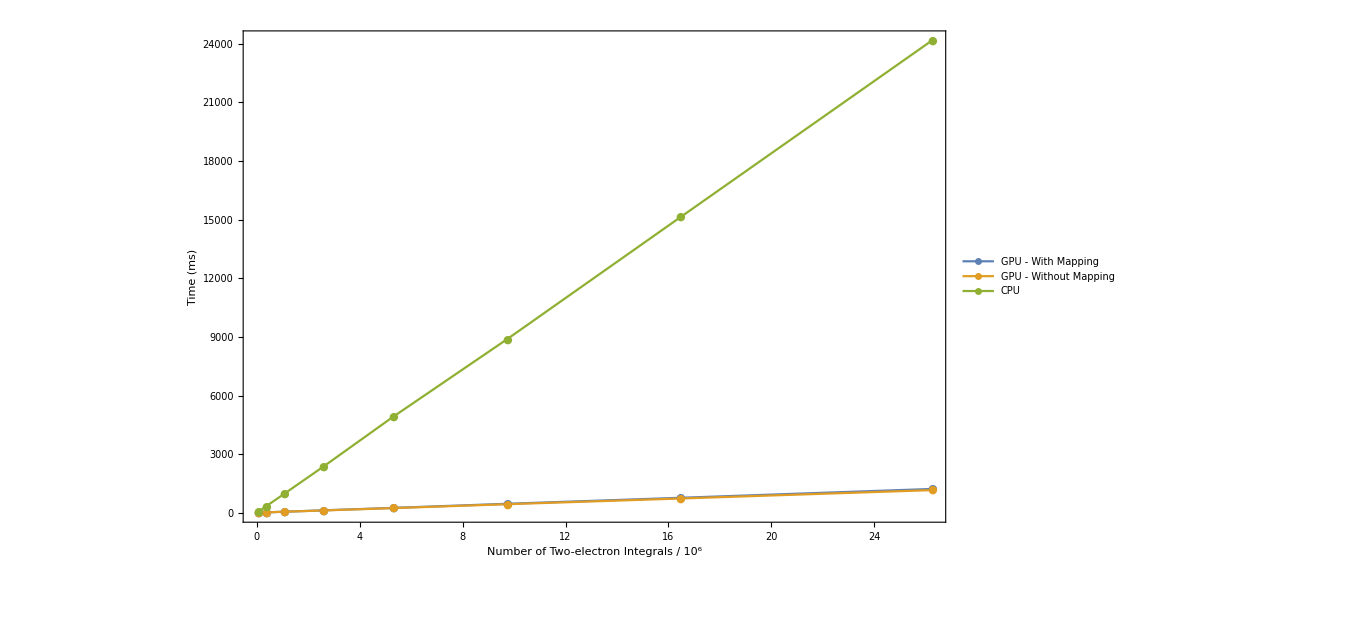

/Users/dylan/thesis/pres_figs/2eint_pro.pdf

```mathematica
(*2eint*)ListLinePlot[{Transpose[{n2eints/10^6, (eint2gpuT + lmpqrsArrayT)}],Transpose[{n2eints/10^6, eint2gpuT}],Transpose[{n2eints/10^6, eint2cpuT}]}, Frame->True,PlotRange->All,FrameLabel->{"Number of Two-electron Integrals / 10^6", "Time (ms)"},ImageSize->1000,BaseStyle->{FontSize->15},LabelStyle->Black,PlotLegends->Placed[{"GPU - With Mapping", "GPU - Without Mapping","CPU"},{0.85,0.5}],PlotMarkers->"●"]
Export["/Users/dylan/thesis/pres_figs/2eint_pro.pdf",
ListLinePlot[{Transpose[{n2eints/10^6, (eint2gpuT + lmpqrsArrayT)}],Transpose[{n2eints/10^6, eint2gpuT}],Transpose[{n2eints/10^6, eint2cpuT}]}, Frame->True,PlotRange->All,FrameLabel->{"Number of Two-electron Integrals / 10^6", "Time (ms)"},ImageSize->1000,BaseStyle->{FontSize->15},LabelStyle->Black,PlotLegends->Placed[{"GPU - With Mapping", "GPU - Without Mapping","CPU"},{0.85,0.5}],PlotMarkers->"●"]
]
```

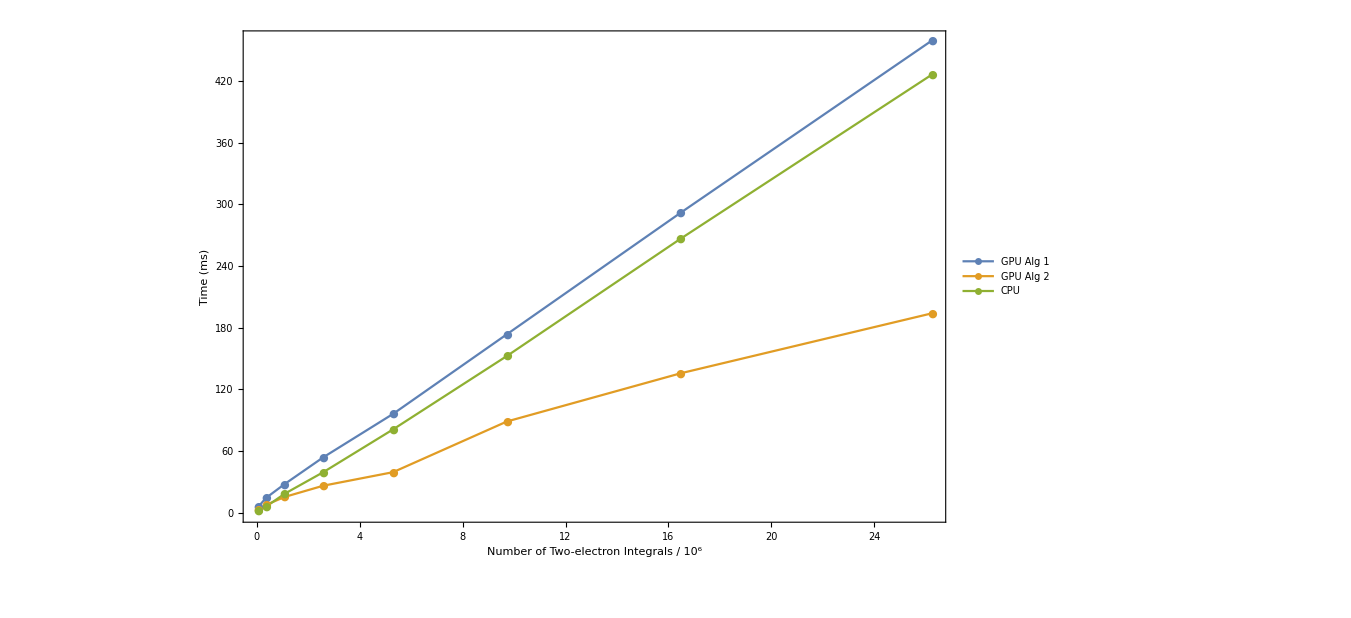

```mathematica
(*Formpq algs*)ListLinePlot[{Transpose[{n2eints/10^6, formpqGpuNewT}],Transpose[{n2eints/10^6, formpqGpuOldT}],Transpose[{n2eints/10^6, formpqCpuT/formpqCpuIter}]}, Frame->True,FrameLabel->{"Number of Two-electron Integrals / 10^6", "Time (ms)"},ImageSize->1000,BaseStyle->{FontSize->15},LabelStyle->Black,PlotLegends->Placed[{"GPU Alg 1","GPU Alg 2","CPU"},{0.85,0.5}],PlotMarkers->"●"]
```

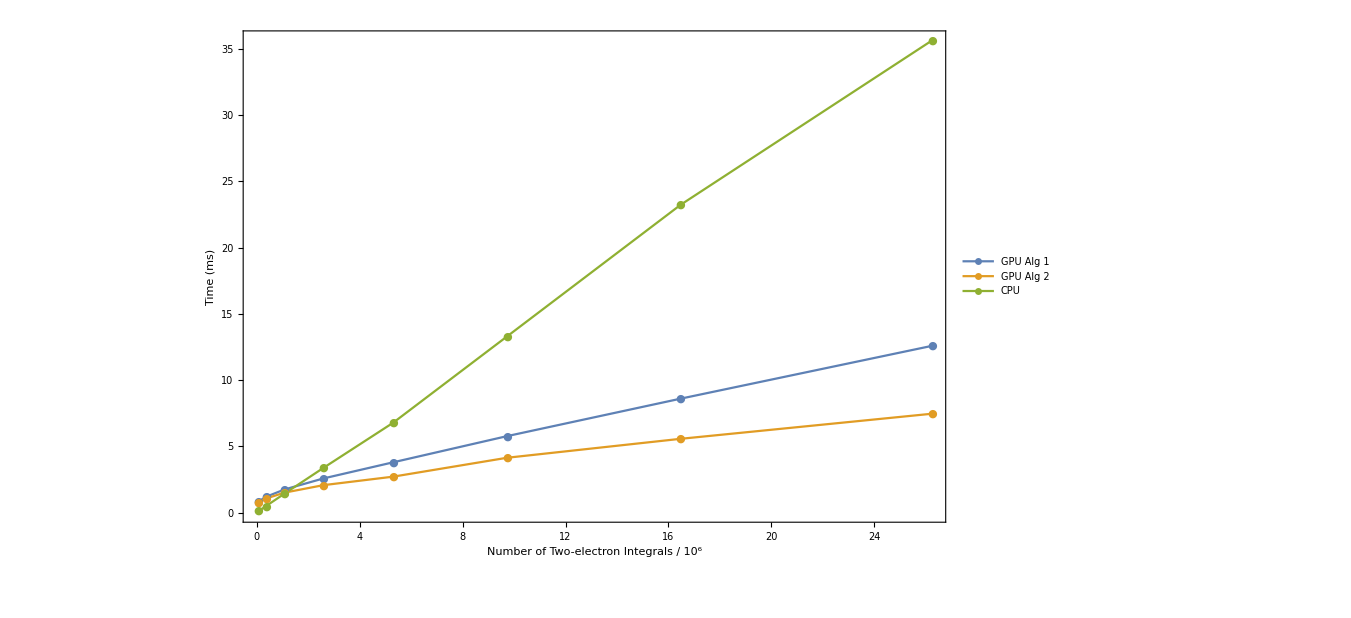

```mathematica
(*total time*)ListLinePlot[{Transpose[{n2eints/10^6, GpuTotalNewT}],Transpose[{n2eints/10^6, GpuTotalOldT}],Transpose[{n2eints/10^6, cpuTotalT}]}, Frame->True,FrameLabel->{"Number of Two-electron Integrals / 10^6", "Time (ms)"},ImageSize->1000,BaseStyle->{FontSize->15},LabelStyle->Black,PlotLegends->Placed[{"GPU Alg 1","GPU Alg 2","CPU"},{0.85,0.5}],PlotMarkers->"●",PlotRange->All]
```

```mathematica
cpuTotalT/GpuTotalOldT
```

{0.158568,0.460748,0.950593,1.62422,2.49302,3.20588,4.16455,4.76964}

## Block Layout

```mathematica
blankBox[x_,y_]:={EdgeForm[Thin],White,Rectangle[{x,y}]}
blockM[x_,y_]:={EdgeForm[{Thick,Orange}],Transparent,Rectangle[{x,y+1},{x+16,y-15}]}
blockV[x_,y_,length_]:={EdgeForm[{Thick,Orange}],Transparent,Rectangle[{x,y+1},{x+length,y}]}
workload[l_,x_,y_,work_]:={White,Cuboid[{x,y,0},{x+1 ,y+1,work*.01}]}
```

```mathematica
nbs=70;
x=0;
y=0;
ymax=-1;
all={};
For[r=1,r≤nbs,r++,
For[s=1,s≤r,s++,
If[y==ymax,y=0;x++;ymax--;];
all=Append[all,blankBox[x,y]];
y--;
]
]
For[x=0,x<nbs,x+=16,
For[y=0,y>-nbs,y-=16,
all=Append[all,blockM[x,y]];
]
]
Graphics[all,ImageSize->1000]
```

-Graphics-

```mathematica
nbs=69;
x=0;
y=0;
xmax=127;
all={};
For[r=1,r≤nbs,r++,
For[s=1,s≤r,s++,
all=Append[all,blankBox[x,y + (0.75*y)]];
If[x==xmax,y--;x=0,x++;];
]
]
For[y=0,y>-Floor[(((nbs + 1) * nbs/2)/127  )],y--,
For[x=0,x<xmax,x+=32,
all=Append[all,blockV[x,y+ (0.75*y),32]];
]
]

Graphics[all,ImageSize->2000]
```

-Graphics-

```mathematica
nbs={30,25,25,20,20,15,15};
numints=ConstantArray[0,{7,32,32}];
For[l=1,l≤7,l++,
For[p=1,p≤nbs[[l]],p++,
For[q=1,q≤p,q++,
i=0;
For[m=1,m≤l,m++,
If[l==m,maxr=p,maxr=nbs[[m]]];
For[r=1,r≤maxr,r++,
If[(l==m) &&(p==r),maxs=q,maxs=r];
For[s=1,s≤maxs,s++,
i++;
]
]
];
numints[[l,p,q]]=i;
]
]
]
```

```mathematica
graph={};
For[l=0,l<7,l++,
all={};
For[y=1,y<33,y++,
For[x=1,x<33,x++,
all=Append[all,workload[l,x,y,numints[[l+1,x,y]]]];
]
];
graph=Append[graph,Graphics3D[all,Axes->True,ViewPoint->{-2, 1.9, 0.75},AxesLabel->{"threadIdx.y","threadIdx.z","Number of Integrals / 10^2"},BaseStyle->{FontSize->25,"Times"},LabelStyle->Black,ImageSize->{1000,500}]];
]
GraphicsGrid[
{{graph[[1]],graph[[2]],graph[[3]]},
{graph[[4]],graph[[5]],graph[[6]]},
{graph[[7]]}
}]
Export["/Users/dylan/thesis/pres_figs/naive_layout.pdf",
GraphicsGrid[
{{graph[[1]],graph[[2]],graph[[3]]},
{graph[[4]],graph[[5]],graph[[6]]},
{graph[[7]]}
}]
]
```

-Graphics-

/Users/dylan/thesis/pres_figs/naive_layout.pdf

## GPU arc

```mathematica
gpu[xmin_,ymin_,xmax_,ymax_]:={{EdgeForm[Thin], gpuColour, Rectangle[{xmin, ymin}, {xmax , ymax}]},
{EdgeForm[Thin],gmemColour, Rectangle[{xmin+0.1*(xmax-xmin),ymin},{xmax-0.1*(xmax-xmin), ymin + 0.25*(ymax-ymin)}]}}
threads[threadPerRow_,threadPerCol_, xmin_, ymin_, xmax_, ymax_]:=Module[{allThreads, i, j,offsetX, offsetY, threadxmin, threadxmax, threadymin,threadymax,ySpace, threadsize,avXspace, avYspace},
allThreads = {};
offsetX = 0.1;
offsetY= 0.;
ySpace = (ymax - ymin) *0.30;
avXspace = xmax - xmin -2*offsetX;
avYspace = ymax - ymin -2*offsetY - ySpace;
If[(avXspace/threadPerRow) ≥ (avYspace/threadPerCol), threadsize =avYspace/threadPerCol, threadsize=  avXspace/threadPerRow];
offsetX = ((xmax - xmin) - (threadsize * threadPerRow))/2;
For[i = 0, i<threadPerCol, i++,
For[j=0, j < threadPerRow, j++,
threadxmin=(xmin + offsetX) + j *threadsize;
threadxmax =threadxmin+ threadsize;
threadymin = (ymin +offsetY+ ySpace) + i  *threadsize;
threadymax=threadymin + threadsize;

allThreads = Append[allThreads, {EdgeForm[Thin], threadColour, Rectangle[{threadxmin,threadymin},{threadxmax,threadymax}]}];
allThreads = Append[allThreads, {Black, Text["("<>ToString[j+1]<> ToString[", "]<> ToString[threadPerCol-i ]<>")",{(threadxmin+ threadxmax)/2,(threadymin+ threadymax)/2  + 0.1*threadsize},BaseStyle->{FontSize->15,FontFamily->"Times"}]}];
allThreads = Append[allThreads, {EdgeForm[Thin], rmemColour, Rectangle[{threadxmin +0.1*threadsize,threadymin},{threadxmax-0.1*threadsize,threadymin + 0.25*threadsize}]}];
]
];
allThreads
]
block[blockPerRow_,blockPerCol_, threadPerRow_,threadPerCol_,xmin_, ymin_, xmax_, ymax_]:=Module[{allBlocks, i, j,offsetX, offsetY, blockxmin, blockxmax, blockymin, blockymax,ySpace},
allBlocks = {};
offsetX = 0.25;
offsetY= 0.25;
ySpace = (ymax - ymin) / 4;
For[i = 0, i<blockPerCol, i++,
For[j=0, j < blockPerRow, j++,
blockxmin = xmin + j *(xmax / blockPerRow )+ offsetX;
blockymin = (ymin+ySpace) + i * ((ymax - (ySpace + ymin))/blockPerCol )+ offsetY;
blockxmax = xmin + (j + 1) *(xmax / blockPerRow )- offsetX;
blockymax=(ymin+ySpace) + (i+1) * ((ymax -( ySpace + ymin))/blockPerCol )- offsetY ;

allBlocks = Append[allBlocks, {EdgeForm[Thin], blockColour, Rectangle[{blockxmin,blockymin},{blockxmax,blockymax}]}];
allBlocks = Append[allBlocks, threads[threadPerRow,threadPerCol,blockxmin, blockymin, blockxmax, blockymax]];
allBlocks = Append[allBlocks, {Black, Text["("<>ToString[j+1]<> ToString[", "]<> ToString[blockPerCol-i ]<>")",{(blockxmin+ blockxmax)/2,blockymin+ (blockymax-blockymin)*0.9},BaseStyle->{FontSize->20,FontFamily->"Times"}]}];
allBlocks = Append[allBlocks, {EdgeForm[Thin], smemColour, Rectangle[{blockxmin +0.1*(blockxmax-blockxmin),blockymin},{blockxmax-0.1*(blockxmax-blockxmin),blockymin + 0.25*(blockymax - blockymin)}]}];
]
];
allBlocks
]
```

```mathematica
xmin=0;
ymin=0;
xmax=9;
ymax=12;
blockPerRow=2;
blockPerCol=2;
threadPerRow=8;
threadPerCol=4;
gpuColour=RGBColor[0,0,1];
blockColour=RGBColor[0,0.5,1];
threadColour=RGBColor[0,1,1];
gmemColour=RGBColor[1,0,0];
smemColour=RGBColor[1,0.5,0];
rmemColour=RGBColor[1,1,0];

Rasterize[Graphics[{gpu[xmin, ymin, xmax, ymax],block[blockPerRow, blockPerCol,threadPerRow,threadPerCol, xmin, ymin, xmax, ymax]},ImageSize->800]]
```

-Graphics-